ΜΣΜ 61  
3η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

α)

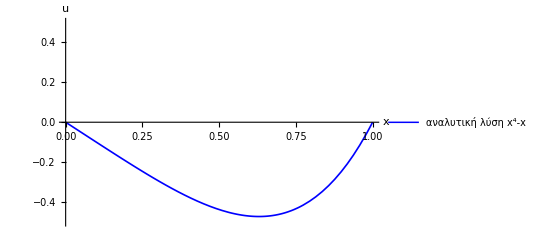

```mathematica
Clear["Global`*"]
ode=u''[x]==12*x^2;
bc1=u[0]==0;
bc2=u[1]==0;
sol1=DSolve[{ode,bc1,bc2},u[x],x];
Plot[u[x]/.sol1,{x,0,1},AxesOrigin->{0,0},PlotRange->{-0.5,0.5}, PlotStyle->{Blue, Thickness[0.003]},ImageSize->Scaled[0.5],AxesLabel->{x,u} ,PlotLegends->{ "αναλυτική λύση   x^4-x  "}]
```

β)

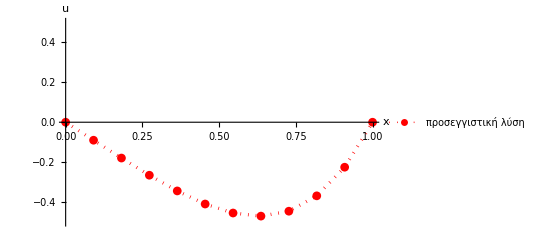

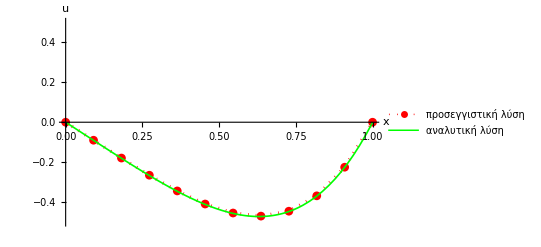

```mathematica
Clear["Global`*"]
f[x_]:=12*x^2
exact[x_]:= x^4-x
ax=0;
bx=1;
n=10;
h=1/(n+1);
u[0]=0;
u[n+1]=0;

vars=Table[  u[i],{i,1,n}];
equ[i_Integer] :=(u[i+1]-2u[i]+u[i-1])/h^2==f[i*h]
eqns=Table[equ[i],{i,1,n}];
sol2=Solve[eqns,vars];


list=Table[{ax+i*h,u[i]},{i,0,n+1}]/.sol2;
pts=Flatten[list,1] ;
p1=ListPlot[pts,Joined->True,PlotMarkers->Automatic,Mesh->All,AxesOrigin->{0,0},PlotStyle->{Red,Dotted,Thickness[0.006]},PlotRange->{-0.5,0.5}, AxesLabel->{x,u} ,AxesStyle->Directive[Purple,15],PlotLegends->{ "προσεγγιστικ:03ae λ:03cdση"}]
p2=Plot[exact[x],{x,ax,bx},AxesOrigin->{0,0},PlotRange->{-0.5,0.5}, PlotStyle->{Green, Thickness[0.003]},AxesLabel->{x,u} ,AxesStyle->Directive[Purple,15],PlotLegends->{ "αναλυτικ:03ae λ:03cdση   "}];
Show[p1,p2]
```

γ)

```mathematica
data=Table[{ax+i*h,N[u[i]/.sol2],N[exact[ax+i*h]]},{i,0,n+1}];
td=TableForm[data,TableSpacing->{1.5,10},TableAlignments->Center,TableHeadings ->{None,{"x" ,"προσεγγιστικ:03ae τιμ:03ae","ακριβ:03aeς τιμ:03ae "}}]
```

x | προσεγγιστική τιμή | ακριβής τιμή 
0 | 0. | 0.
1/11 | -0.0901578 | -0.0908408
2/11 | -0.179496 | -0.180725
3/11 | -0.265556 | -0.267195
4/11 | -0.344239 | -0.346151
5/11 | -0.409808 | -0.411857
6/11 | -0.454887 | -0.456936
7/11 | -0.47046 | -0.472372
8/11 | -0.445871 | -0.44751
9/11 | -0.368827 | -0.370057
10/11 | -0.225394 | -0.226077
1 | 0. | 0.

δ)

```mathematica
L2=Sqrt[Integrate[ (x^4-x )^2 ,{x,0,1}]];
Lh= Sqrt[h*Sum[(u[k]/.sol2 )^2 ,{k,1,n}] ]//N;
Print["\n• Nόρμα αναλυτικής λύσης : ",L2]
Print["\n• Διακριτή νόρμα  προσεγγιστικής λύσης : ",Lh[[1]]]
Print["\n• Απόλυτη τιμη διαφοράς : ",Abs[L2-Lh][[1]]]
Print["\n"]
```

• Nόρμα αναλυτικής λύσης : 1/3

• Διακριτή νόρμα  προσεγγιστικής λύσης : 0.331827

• Απόλυτη τιμη διαφοράς : 0.00150619

Ασκηση 2

α)

```mathematica
Clear["Global`*"]
s1=DSolve[{u''[x]== -u[x],u[0]==1,u[Pi/2]==1},u[x],x];
ExactSolution[x_]=s1[[1,1,2]];
Print["H λύση της εξίσωσης είναι : ",ExactSolution[x]]
```

H λύση της εξίσωσης είναι : Cos[x]+Sin[x]

β)

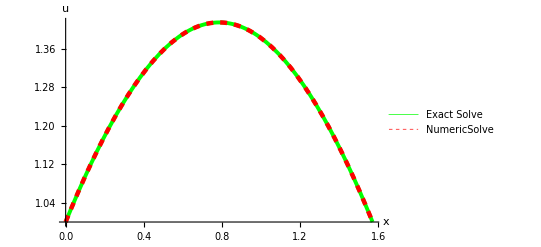

```mathematica
s2=NDSolve[{u''[x]== -u[x],u[0]==1,u[Pi/2]==1},u[x],{x,0,Pi/2}];
NumericSolution[x_]=s2[[1,1,2]];
p2=Plot[NumericSolution[x],{x,0,Pi/2},PlotStyle->{Red,Dashed,Thickness[0.008]},PlotLegends->{ "NumericSolve"},AxesLabel->{x,u}];
p1=Plot[ExactSolution[x],{x,0,Pi/2},PlotStyle->{Green,Thickness[0.007]},PlotLegends->{ "Exact Solve"},AxesLabel->{x,u}];
Show[p1,p2]
```

γ)

```mathematica
L1=1/16*Sum[Abs[NumericSolution[0.1k]-ExactSolution[0.1k]],{k,0,15}];
L2=√(1/16*Sum[( NumericSolution[0.1k]-ExactSolution[0.1k])^2,{k,0,15}]) ;
Print[ "µ:03adσο απ:03ccλυτο σφ:03acλµα   L1 = " , L1]
Print[ "µ:03adσο τετραγωνικ:03cc σφ:03acλµα L2 = " ,L2]

data=Table[ {0.1i,ExactSolution[0.1i],NumericSolution[0.1i],Abs[NumericSolution[0.1i]-ExactSolution[0.1i]] ,{}}  ,   {i,0,15}] ;
TableForm[data, TableAlignments->Center,TableHeadings->{{},{"κ:03ccμβος x_i","ακριβ:03aeς τιμ:03ae ","προσεγγιστικ:03ae τιμ:03ae","απ:03ccλυτο σφ:03acλμα", "L1 =",L1 ,"&",  "L2 =",L2 }}]
```

µέσο απόλυτο σφάλµα   L1 = 3.83517×10^-8

µέσο τετραγωνικό σφάλµα L2 = 4.45165×10^-8

| κόμβος x_i | ακριβής τιμή  | προσεγγιστική τιμή | απόλυτο σφάλμα | L1 = | 3.83517×10^-8 | & | L2 = | 4.45165×10^-8
 | 0. | 1. | 1. | 0. |  |  |  |  | 
 | 0.1 | 1.09484 | 1.09484 | 1.04277×10^-9 |  |  |  |  | 
 | 0.2 | 1.17874 | 1.17874 | 6.77151×10^-9 |  |  |  |  | 
 | 0.3 | 1.25086 | 1.25086 | 3.71031×10^-9 |  |  |  |  | 
 | 0.4 | 1.31048 | 1.31048 | 2.47179×10^-8 |  |  |  |  | 
 | 0.5 | 1.35701 | 1.35701 | 3.36142×10^-8 |  |  |  |  | 
 | 0.6 | 1.38998 | 1.38998 | 4.3107×10^-8 |  |  |  |  | 
 | 0.7 | 1.40906 | 1.40906 | 6.34337×10^-8 |  |  |  |  | 
 | 0.8 | 1.41406 | 1.41406 | 6.16028×10^-8 |  |  |  |  | 
 | 0.9 | 1.40494 | 1.40494 | 5.68956×10^-8 |  |  |  |  | 
 | 1. | 1.38177 | 1.38177 | 5.5702×10^-8 |  |  |  |  | 
 | 1.1 | 1.3448 | 1.3448 | 5.58529×10^-8 |  |  |  |  | 
 | 1.2 | 1.2944 | 1.2944 | 5.53708×10^-8 |  |  |  |  | 
 | 1.3 | 1.23106 | 1.23106 | 5.36969×10^-8 |  |  |  |  | 
 | 1.4 | 1.15542 | 1.15542 | 5.10121×10^-8 |  |  |  |  | 
 | 1.5 | 1.06823 | 1.06823 | 4.70961×10^-8 |  |  |  |  |

Ασκηση 3

α)

Για n=24:

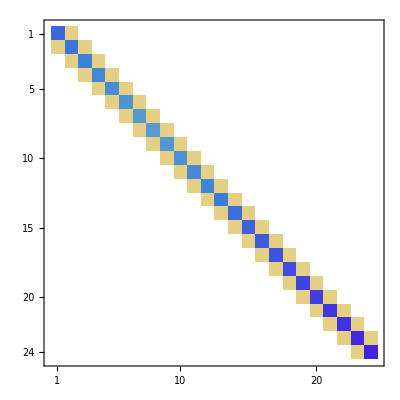

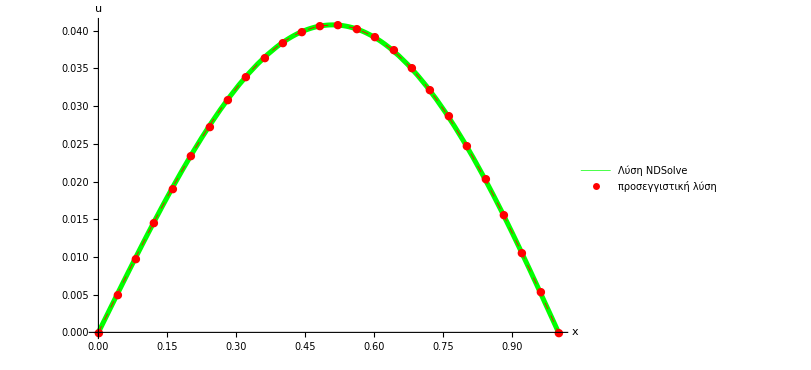

Για n=120:

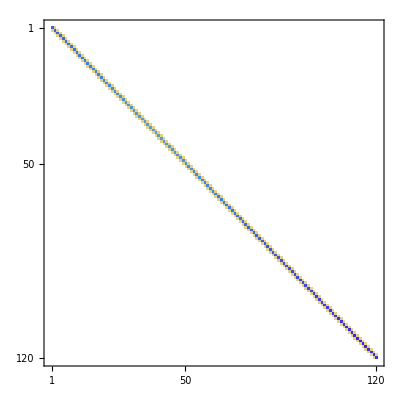

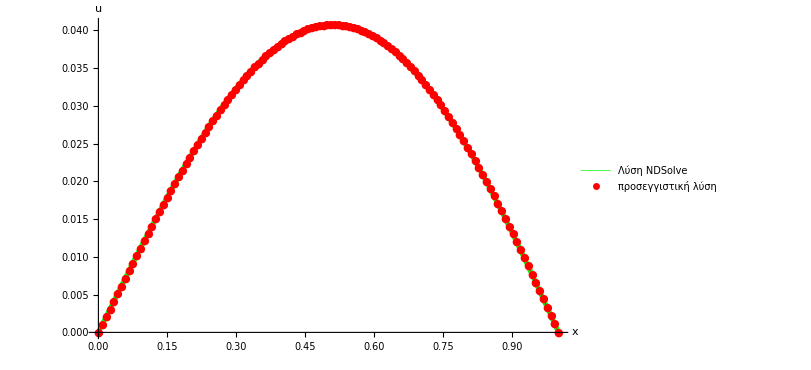

```mathematica
Clear["Global`*"]

(*Εύρεση λύσης με την μέθοδο NDSolve*)
s1=NDSolve[{u''[x]+Sin[5*x]*u[x]== x^3-x,u[0]==0,u[1]==0},u[x],{x,0,1}];
ExactSolution[x_]=s1[[1,1,2]];
Graph1=Plot[ExactSolution[x],{x,0,1},PlotRange->All,PlotStyle->{Green,Thickness[0.006]},PlotLegends->{ "Λύση NDSolve"},AxesLabel->{x,u},ImageSize->{600,400}];


(*Συνάρτηση που υπολογίζει την λύση με την μέθοδο πεπ. διαφορών, δέχεται σαν όρισμα το n*)
SolveFunction[n_]:=(
f[x_]:= x^3-x;
ax=0;
bx=1;
u[0]=0;
u[n+1]=0;
 h=(bx-ax)/(n+1);
equ[i_Integer] :=2*u[i+1]-(4-2*h^2*Sin[5*i*h])*u[i]+2*u[i-1]==2*h^2*f[i*h];
eqns1=Table[equ[i ],{i,1,n}] ;
eqns=Expand[eqns1];
system=Normal[CoefficientArrays[eqns ] ];
A=system[[2]];
b=system[[1]]//N;
systemsol=LinearSolve[A,-b]//N;
Do[(u[i]=systemsol[[i]]),{i,1,n }];
pts=Table[{ax+i*h,u[i]},{i,0,n+1}];
Graph2=ListPlot[pts,Joined->True,PlotMarkers->{Automatic,Medium},Mesh->All,PlotStyle->{Red,Dashed,Thickness[0.001]},AxesLabel->{x,u} ,PlotLegends->{ "προσεγγιστικ:03ae λ:03cdση"}];
)

(*Yπολογισμός της λύσης για n=24*)
SolveFunction[24]
Print["\nΓια n=24:"]
MatrixPlot[A]
Show[Graph1,Graph2]

Clear[u]

(*Yπολογισμός της λύσης για n=120*)
SolveFunction[120]
Print["\nΓια n=120:"]
MatrixPlot[A]
Show[Graph1,Graph2]
```

β)

```mathematica
(*Υπολογίζουμε τις νόρμες για την τελευταία φορά που τρέξαμε το πρόγραμμα δηλαδή για n=120*)
n=120;

Luh= Sqrt[h*Sum[u[k]^2 ,{k,1,n}] ] ;
Lu1h= Sqrt[h*Sum[((u[k+1]-u[k])/h)^2 ,{k,0,n}] ];
Print["Nόρμα προσεγγιστικής λύσης ||u(||)_h  =",Luh]
Print["Nόρμα παραγώγου προσεγγιστικής λύσης ||u(||)_(1, h)  =",Lu1h]
```

Nόρμα προσεγγιστικής λύσης ||u(||)_h  =0.028849

Nόρμα παραγώγου προσεγγιστικής λύσης ||u(||)_(1, h)  =0.0906696

```mathematica
(*Eπιβεβαιώνουμε την ανισότητα poincare friedrichs*)
Luh<=(1/(2*Sqrt[2]) )*Lu1h
```

True

Ασκηση 4

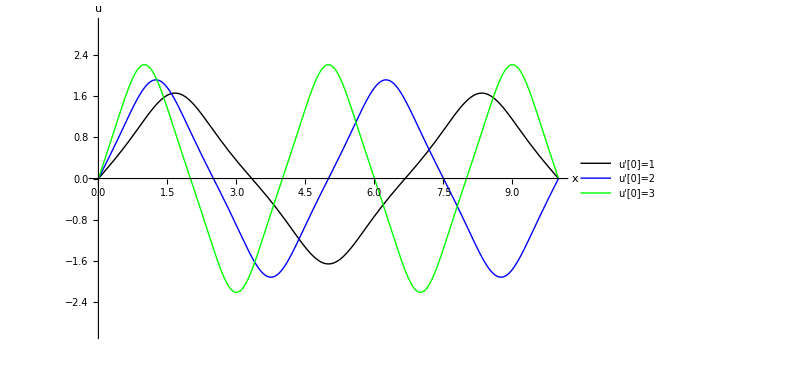

```mathematica
Clear["Global`*"]

sols = Map[First[NDSolve[{U''[x]  ==  U[x]-U[x]^3,U[0] ==U[10] == 0},U,x, Method->{"Shooting", "StartingInitialConditions"->{U[0] == 0,U'[0] == #}}]]&,{1,2,3}];
Graph1=Plot[Evaluate[U[x] /. sols], {x,0,10},PlotLegends->{"u'[0]=1","u'[0]=2","u'[0]=3"},PlotRange->{-3,3},AxesLabel->{x,u}, PlotStyle->{Black, Blue, Green,Red},ImageSize->{600,400}]
```

Παρατηρούμε ότι ένα μη γραμμικό ΠΣΤ όπως το παραπάνω  μπορεί να έχει άπειρες λύσεις οι οποίες εξαρτώνται από την τιμή u’[0]

Ασκηση 5

α)

```mathematica
Clear["Global`*"]
u[x_,y_]:=x*(1-x)*y*(1-y)
f[x_,y_]:=-(2x(1-x)+2y(1-y))
s1=D[u[x,y],{x,2}];
s2=D[u[x,y],{y,2}];

(*Βρίσκουμε ότι η παρακάτω σχέση αληθεύει*)
s1+s2==f[x,y]
u[0,y]
u[1,y]
u[x,0]
u[x,1]
```

True

0

0

0

«1 more identical outputs»

β)

-Graphics3D-

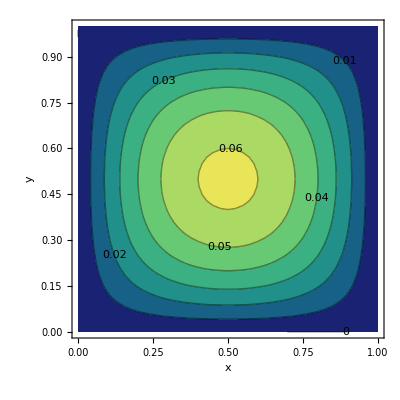

-Graphics3D-

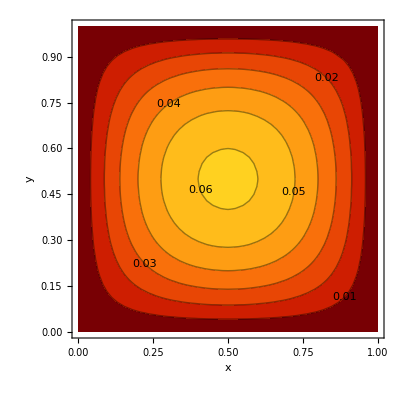

```mathematica
Clear ["Global`*"]

f[x_,y_]:=-(2x(1-x)+2y(1-y))
(*Μπορούμε να μεγαλώσουμε το n για περισσότερη ακρίβεια.*)
 n=9;
h=1/(n+1);

(*αρχικές συνθήκες*)
u[0,j_]=0 ;
u[n+1,j_]=0 ;
u[i_,0]=0 ;
u[i_,n+1]=0 ;
nod=  Table[  u[i,j],{i,0,n+1},{j,0,n+1} ] //Flatten;

(*Μέθοδος πεπερασμένων διαφορών*)
equ[i_Integer,j_Integer]=(u[i+1,j ]+u[i-1,j ]+u[i,j-1]+u[i,j+1]-4 u[i,j]==h^2 *f[i* h,j* h]);
eqns=Flatten[Table[equ[i,j],{i,1,n},{j,1,n}] ];
vars=Flatten[Table[  u[i,j],{i,1,n},{j,1,n} ]];
system  = Normal[CoefficientArrays[eqns,vars]] ; 
A= system[[2]];
b= system[[1]]//N;
MatrixForm[A] ;
MatrixForm[b] ; 

(*επίλυση του συστήματος*)
sysol=LinearSolve[A,-b]//N;
  sol={};
Do [  sol=Append[sol,vars[[k]]->sysol[[k]]],{k,1,Length[eqns]}]
 Table[sol [[k]],{k,1,Length[eqns]}]//TableForm;

(*γραφική παράσταση προσεγγιστικής λύσης*)
numsol= Interpolation[
Flatten[ Table[{0+i*h, 0+j*h, u[i,j]}, {i,0,n+1},{j,0,n+1}]/.sol ,1  ]  ];
p1=Plot3D[numsol[x,y], {x,0,1}, {y,0,1},PlotPoints->100,ColorFunction->"BlueGreenYellow",AxesLabel->Automatic,ImageSize->Scaled[.4] ]
 ContourPlot[ numsol[x,y], {x,0,1}, {y,0,1}, ColorFunction->"BlueGreenYellow", FrameLabel->{"x","y"}, ContourLabels-> True,ImageSize->Scaled[.4] ]

(*γραφική παράσταση αναλυτικής λύσης*)
solution[x_,y_]:=x*(1-x)*y*(1-y)
 Plot3D[solution[x,y], {x,0,1}, {y,0,1},AxesLabel->Automatic,PlotPoints->100,ColorFunction->ColorData["SolarColors"],ImageSize->Scaled[.4] ] 
 ContourPlot[ solution[x,y], {x,0,1}, {y,0,1}, FrameLabel->{"x","y"},ColorFunction->ColorData["SolarColors"], ContourLabels-> True,ImageSize->Scaled[.4] ]
```

γ)

```mathematica
data1=Table[  {0.1i,0.1j }     ,{j,0,10},{i,0,10}]   ;
data2=Table[  numsol[0.1i,0.1j]     ,{j,0,10},{i,0,10}]    ;
data3=Table[  solution[0.1i,0.1j]   ,{j,0,10},{i,0,10}]   ;
data4=Table[Abs[numsol[0.1i,0.1j]-solution[0.1i ,0.1j]] ,{j,0,10},{i,0,10}] ;
TableForm[{data1,data2,data3 ,data4}, TableAlignments->Center,TableSpacing->{4,3},TableHeadings->{{"κ:03ccμβος ", "προσ. τιμ:03ae" ,"ακριβ:03aeς τιμ:03ae ","σφ:03acλμα"},Automatic}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
κόμβος  | 0. | 0.
0.1 | 0.
0.2 | 0.
0.3 | 0.
0.4 | 0.
0.5 | 0.
0.6 | 0.
0.7 | 0.
0.8 | 0.
0.9 | 0.
1. | 0. | 0. | 0.1
0.1 | 0.1
0.2 | 0.1
0.3 | 0.1
0.4 | 0.1
0.5 | 0.1
0.6 | 0.1
0.7 | 0.1
0.8 | 0.1
0.9 | 0.1
1. | 0.1 | 0. | 0.2
0.1 | 0.2
0.2 | 0.2
0.3 | 0.2
0.4 | 0.2
0.5 | 0.2
0.6 | 0.2
0.7 | 0.2
0.8 | 0.2
0.9 | 0.2
1. | 0.2 | 0. | 0.3
0.1 | 0.3
0.2 | 0.3
0.3 | 0.3
0.4 | 0.3
0.5 | 0.3
0.6 | 0.3
0.7 | 0.3
0.8 | 0.3
0.9 | 0.3
1. | 0.3 | 0. | 0.4
0.1 | 0.4
0.2 | 0.4
0.3 | 0.4
0.4 | 0.4
0.5 | 0.4
0.6 | 0.4
0.7 | 0.4
0.8 | 0.4
0.9 | 0.4
1. | 0.4 | 0. | 0.5
0.1 | 0.5
0.2 | 0.5
0.3 | 0.5
0.4 | 0.5
0.5 | 0.5
0.6 | 0.5
0.7 | 0.5
0.8 | 0.5
0.9 | 0.5
1. | 0.5 | 0. | 0.6
0.1 | 0.6
0.2 | 0.6
0.3 | 0.6
0.4 | 0.6
0.5 | 0.6
0.6 | 0.6
0.7 | 0.6
0.8 | 0.6
0.9 | 0.6
1. | 0.6 | 0. | 0.7
0.1 | 0.7
0.2 | 0.7
0.3 | 0.7
0.4 | 0.7
0.5 | 0.7
0.6 | 0.7
0.7 | 0.7
0.8 | 0.7
0.9 | 0.7
1. | 0.7 | 0. | 0.8
0.1 | 0.8
0.2 | 0.8
0.3 | 0.8
0.4 | 0.8
0.5 | 0.8
0.6 | 0.8
0.7 | 0.8
0.8 | 0.8
0.9 | 0.8
1. | 0.8 | 0. | 0.9
0.1 | 0.9
0.2 | 0.9
0.3 | 0.9
0.4 | 0.9
0.5 | 0.9
0.6 | 0.9
0.7 | 0.9
0.8 | 0.9
0.9 | 0.9
1. | 0.9 | 0. | 1.
0.1 | 1.
0.2 | 1.
0.3 | 1.
0.4 | 1.
0.5 | 1.
0.6 | 1.
0.7 | 1.
0.8 | 1.
0.9 | 1.
1. | 1.
προσ. τιμή | 0.
0.
0.
0.
0.
0.
3.20988×10^-34
-1.92593×10^-33
-1.73472×10^-18
0.
0. | 0.
0.0081
0.0144
0.0189
0.0216
0.0225
0.0216
0.0189
0.0144
0.0081
0. | 0.
0.0144
0.0256
0.0336
0.0384
0.04
0.0384
0.0336
0.0256
0.0144
0. | 0.
0.0189
0.0336
0.0441
0.0504
0.0525
0.0504
0.0441
0.0336
0.0189
0. | 0.
0.0216
0.0384
0.0504
0.0576
0.06
0.0576
0.0504
0.0384
0.0216
0. | 0.
0.0225
0.04
0.0525
0.06
0.0625
0.06
0.0525
0.04
0.0225
0. | 0.
0.0216
0.0384
0.0504
0.0576
0.06
0.0576
0.0504
0.0384
0.0216
0. | 0.
0.0189
0.0336
0.0441
0.0504
0.0525
0.0504
0.0441
0.0336
0.0189
0. | 0.
0.0144
0.0256
0.0336
0.0384
0.04
0.0384
0.0336
0.0256
0.0144
0. | 0.
0.0081
0.0144
0.0189
0.0216
0.0225
0.0216
0.0189
0.0144
0.0081
0. | 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
ακριβής τιμή  | 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0. | 0.
0.0081
0.0144
0.0189
0.0216
0.0225
0.0216
0.0189
0.0144
0.0081
0. | 0.
0.0144
0.0256
0.0336
0.0384
0.04
0.0384
0.0336
0.0256
0.0144
0. | 0.
0.0189
0.0336
0.0441
0.0504
0.0525
0.0504
0.0441
0.0336
0.0189
0. | 0.
0.0216
0.0384
0.0504
0.0576
0.06
0.0576
0.0504
0.0384
0.0216
0. | 0.
0.0225
0.04
0.0525
0.06
0.0625
0.06
0.0525
0.04
0.0225
0. | 0.
0.0216
0.0384
0.0504
0.0576
0.06
0.0576
0.0504
0.0384
0.0216
0. | 0.
0.0189
0.0336
0.0441
0.0504
0.0525
0.0504
0.0441
0.0336
0.0189
0. | 0.
0.0144
0.0256
0.0336
0.0384
0.04
0.0384
0.0336
0.0256
0.0144
0. | 0.
0.0081
0.0144
0.0189
0.0216
0.0225
0.0216
0.0189
0.0144
0.0081
0. | 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
σφάλμα | 0.
0.
0.
0.
0.
0.
3.20988×10^-34
1.92593×10^-33
1.73472×10^-18
0.
0. | 0.
1.73472×10^-18
8.67362×10^-18
6.93889×10^-18
3.46945×10^-18
3.46945×10^-18
0.
0.
1.73472×10^-18
1.73472×10^-18
0. | 0.
5.20417×10^-18
1.38778×10^-17
6.93889×10^-18
6.93889×10^-18
0.
0.
6.93889×10^-18
3.46945×10^-18
0.
0. | 0.
0.
6.93889×10^-18
0.
1.38778×10^-17
6.93889×10^-18
6.93889×10^-18
6.93889×10^-18
6.93889×10^-18
6.93889×10^-18
0. | 0.
6.93889×10^-18
1.38778×10^-17
0.
6.93889×10^-18
6.93889×10^-18
1.38778×10^-17
0.
6.93889×10^-18
3.46945×10^-18
0. | 0.
1.38778×10^-17
2.77556×10^-17
2.08167×10^-17
6.93889×10^-18
1.38778×10^-17
0.
0.
6.93889×10^-18
3.46945×10^-18
0. | 0.
1.38778×10^-17
2.08167×10^-17
1.38778×10^-17
6.93889×10^-18
6.93889×10^-18
6.93889×10^-18
1.38778×10^-17
1.38778×10^-17
6.93889×10^-18
0. | 0.
6.93889×10^-18
6.93889×10^-18
6.93889×10^-18
1.38778×10^-17
1.38778×10^-17
6.93889×10^-18
6.93889×10^-18
0.
3.46945×10^-18
0. | 0.
3.46945×10^-18
6.93889×10^-18
6.93889×10^-18
2.08167×10^-17
2.77556×10^-17
2.77556×10^-17
1.38778×10^-17
1.38778×10^-17
8.67362×10^-18
0. | 0.
1.73472×10^-18
3.46945×10^-18
3.46945×10^-18
1.04083×10^-17
1.73472×10^-17
1.38778×10^-17
1.04083×10^-17
1.21431×10^-17
6.93889×10^-18
0. | 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.

Ασκηση 6

α)

```mathematica
Clear["Global`*"]

uxx=(U[i+1,j]-2*U[i,j]+U[i-1,j] )/h^2;
ut= (U[i,j+1]-U[i,j])/k;

(*κάνουμε αντικατάσταση τις προσεγγίσεις στην (Ε) και λύνουμε ως προς U[i,j+1]*)
s1=Solve[ut==v*uxx,U[i,j+1]];
s1=Expand[s1[[1,1,2]]];

(*κάνουμε αντικατάσταση το r=(v k)/h^2 *)
s1=s1/.(v*k/h^2)->r;

Print["Καταλήγουμε στο παρακάτω σχήμα πεπερασμένων διαφορών:"]  
Print["U[i,j+1] = ",Simplify[s1]]
Print["To οποίο είναι το σχήμα (Δ).\n"]
```

Καταλήγουμε στο παρακάτω σχήμα πεπερασμένων διαφορών:

U[i,j+1] = r U[-1+i,j]+(1-2 r) U[i,j]+r U[1+i,j]

To οποίο είναι το σχήμα (Δ).

β)

```mathematica
Clear["Global`*"]
function[nua_,nXa_,nTa_]:={
   s1=Timing
[{
(*Η παρακάτω εντολή ενώνει τα σημεία στην ListPlot*) 
SetOptions[ListPlot,Joined->True];
(*Ορίζουμε την συνάρτηση f(x)*)
f[x_]:=Sin[Pi*x];
(*Ορίζουμε τον αριθμό διαμέρισης και λοιπά στοιχεία*)
{nu=nua,nX=nXa,nT=nTa,l=1,tF=1,h=l/nX,k=tF/nT,r=N[nu*k/h^2]};
Print["• Εκτέλεση προγραμματος για : "]
	     Print["   ν = ",nu,"    N_x = ",nX,"    N_t = ",nT,"    r = ",Style[r,Red,Bold]]
(*Ορίζουμε τον πίνακα με την διαμέριση του χ*)
Table[xN[i]=i*h,{i,0,nX}];
(*Ορίζουμε την αρχική συνθήκη u[i,0]=f[xi]*)
ic=Table[uN[i,0]->f[xN[i]],{i,0,nX}];
(*Ορίζουμε τον πίνακα με την διαμέριση του y*)
	     bc={Table[uN[0,j]->0,{j,0,nT}],Table[uN[nX,j]->0,{j,0,nT}]};
	     ibc=Flatten[{ic,bc}];
(*Ορίζουμε την συνάρτηση επίλυσης σύμφωνα με το σχήμα (Δ) *)
	     fd[i_,j_]:=(1-2*r)*uN[i,j]+r*(uN[i+1,j]+uN[i-1,j]);
(*Βρίσκουμε τις προσεγγιστικές λύσεις*)
	      Do[uN[i,j+1]=fd[i,j]/.ibc,{j,0,nT},{i,1,nX-1}];}

][[1]];
Print["   ▸ Συνολικός χρόνος εκτέλεσης: ",Style[N[s1,4],FontColor->Blue] ," sec\n\n"]
}

function[1,20,800];
function[1,25,800];
function[1,25,1000];
function[1,25,1200];
function[1,25,1400];
(*
MH=Manipulate[ListPlot[Table[{xN[i],uN[i,j]/.ibc},{i,0,nX}],PlotStyle->{Blue,Thickness[0.002]},AxesLabel->{"x","u"},PlotRange->All],{j,0,nT,1}]; *)
```

• Εκτέλεση προγραμματος για :

ν = 1    N_x = 20    N_t = 800    r = 0.5

▸ Συνολικός χρόνος εκτέλεσης: 17.02 sec

• Εκτέλεση προγραμματος για :

ν = 1    N_x = 25    N_t = 800    r = 0.78125

▸ Συνολικός χρόνος εκτέλεσης: 21.12 sec

• Εκτέλεση προγραμματος για :

ν = 1    N_x = 25    N_t = 1000    r = 0.625

▸ Συνολικός χρόνος εκτέλεσης: 32.71 sec

• Εκτέλεση προγραμματος για :

ν = 1    N_x = 25    N_t = 1200    r = 0.520833

▸ Συνολικός χρόνος εκτέλεσης: 47.61 sec

• Εκτέλεση προγραμματος για :

ν = 1    N_x = 25    N_t = 1400    r = 0.446429

▸ Συνολικός χρόνος εκτέλεσης: 65.46 sec

Παρατηρούμε ότι για  N_x=25 , N_t=800  η μέθοδος αποτυγχάνει (δεν είναι ευσταθής). 
Επίσης η μέθοδος αποτυγχάνει για  N_x=25 , N_t=1000 ,1200.
Όμως παρατηρούμε ότι αυξάνοντας το  N_t  η  αποτυχία συμβαίνει για όλο και μεγαλύτερη τιμή του t.
Για N_x=25,  N_t= 1400  παρατηρούμε ότι η μέθοδος επιτυγχάνει!

Όπως αναφέρεται στην ενότητα  <<4.3.1.1 Έλεγχος της Ευστάθειας της Μεθόδου Euler>> 
η τιμή του r δεν πρέπει να είναι μεγαλύτερη από 0.5 για να είναι ευσταθής η μέθοδος,
πράγμα το οποίο επαληθεύεται από τις παραπάνω δοκιμές.

Τέλος οι χρόνοι που απαιτούνται για την παραγωγή των αποτελεσμάτων είναι μεγαλύτεροι 
όσο αυξάνουμε τον αριθμό των διαμερίσεων είτε για το x , είτε για το t .
Αυτό συμβαίνει γιατί αυξάνεται το μέγεθος των πινάκων με αποτέλεσμα να χρειάζονται 
περισσότερες πράξεις άρα και περισσότερος χρόνος.

γ)

```mathematica
Clear["Global`*"]

SolveFunction[syntelestis_]:={
SetOptions[ListPlot,Joined->True];
f[x_]:=Sin[Pi*x];
{nu=syntelestis,nX=20,nT=800,l=1,tF=1,h=l/nX,k=tF/nT,r=N[nu*k/h^2]};
Table[xN[i]=i*h,{i,0,nX}];
Table[tN[j]=j*k,{j,0,nT}];
ic=Table[uN[i,0]->f[xN[i]],{i,0,nX}];
	bc={Table[uN[0,j]->0,{j,0,nT}],Table[uN[nX,j]->0,{j,0,nT}]};
	ibc=Flatten[{ic,bc}];
	fd[i_,j_]:=(1-2*r)*uN[i,j]+r*(uN[i+1,j]+uN[i-1,j]);
	Do[uN[i,j+1]=fd[i,j]/.ibc,{j,0,nT},{i,1,nX-1}] ;

     data=Flatten[Table[{xN[i],tN[j],uN[i,j]/.ibc},{j,0,nT},{i,0,nX}],1];
interpolation3d=Interpolation[data];
}

PlotFunction[nu_]:=
Labeled[
Plot3D[interpolation3d[x,y],{x,0,1},{y,0,1},AxesLabel->{Style[x,Blue,Bold,12],Style[t,Blue,Bold,12],Style[u,Blue,Bold,12]},LabelStyle->Directive[Brown,Opacity[0.7]],ColorFunction->"TemperatureMap",Mesh->4,
ImageSize->Large,PlotRange->{-1,1}],Framed[Style[ {"Συντελεστής διάχυσης",nu},Black,Bold,12],Background->White],{Right},Spacings->5]


SolveFunction[1];
PlotFunction[1]

SolveFunction[0.5];
PlotFunction[0.5]

SolveFunction[0.05];
PlotFunction[0.05]
```

-Graphics3D-{Συντελεστής διάχυσης,1}

-Graphics3D-{Συντελεστής διάχυσης,0.5}

-Graphics3D-{Συντελεστής διάχυσης,0.05}

Παρατηρούμε ότι  ο συντελεστής διάχυσης είναι αντιστρόφος ανάλογος με τον ρυθμό μετάδοσης θερμότητας.
Δηλαδή όσο μικραίνει ο συντελεστής διάχυσης τόσο μεγαλύτερη είναι η ροή θερμότητας.
Για ν=1 έχουμε ένα υλικό που θεωρείτε κακός αγωγός θερμότητας(π.χ. ξύλο).
Ενώ για ν=0.05 έχουμε καλό αγωγό θερμότητας (π.χ. μέταλλο).